```mathematica
(*Mathematica*)
```

```mathematica
Clear[s,w]
```

```mathematica
(*First so(5)*)
s[1]={{0,1,0,0,0},
           {1,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[2]={{0,0,1,0,0},
           {0,0,0,0,0},
          {1,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[3]={{0,0,0,1,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0},
{0,0,0,0,0}};
s[4]={{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0}};
s[5]={{0,0,0,0,0},
{0,0,1,0,0},
{0,1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[10]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,1},
        { 0,0,0,1,0}};
s[9]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,1,0,0}};
s[8]={{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,1,0,0,0}};
s[7]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,1,0},
{0,0,1,0,0},
{0,0,0,0,0}};
s[6]={{0,0,0,0,0},
{0,0,0,1,0},
{0,0,0,0,0},
{0,1,0,0,0},
{0,0,0,0,0}};
(* second so(5) *)
s[11]={{0,I,0,0,0},
           {-I,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[12]={{0,0,-I,0,0},
           {0,0,0,0,0},
          {I,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[13]={{0,0,0,I,0},
{0,0,0,0,0},
{0,0,0,0,0},
{-I,0,0,0,0},
{0,0,0,0,0}};
s[14]={{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{I,0,0,0,0}};
s[15]={{0,0,0,0,0},
{0,0,I,0,0},
{0,-I,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[20]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,I},
        { 0,0,0,-I,0}};
s[19]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,I,0,0}};
s[18]={{0,0,0,0,0},
{0,0,0,0,I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,-I,0,0,0}};
s[17]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,I,0},
{0,0,-I,0,0},
{0,0,0,0,0}};
s[16]={{0,0,0,0,0},
{0,0,0,-I,0},
{0,0,0,0,0},
{0,I,0,0,0},
{0,0,0,0,0}};
(* DIAGONAL four: n-1 matrices*)
(* zero trace with normalization Sqrt[n*(n-1)/2]*)
s[21]={{1,0,0,0,0},
{0,-1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[22]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,-2,0,0},
{0,0,0,0,0},
{0,0,0,0,-1}}/Sqrt[7/2];
s[23]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,-3,0},
{0,0,0,0,0}}/Sqrt[6];
s[24]={{2,0,0,0,0},
{0,2,0,0,0},
{0,0,2,0,0},
{0,0,0,-3,0},
{0,0,0,0,-3}}/√30;
s[25]=IdentityMatrix[5];
```

```mathematica
p[x_]=-1+296 x^6-602 x^12-296 x^18-x^24
```

-1+296 x^6-602 x^12-296 x^18-x^24

```mathematica
r[i_]:=z/.NSolve[p[z]==0,z][[i]]
```

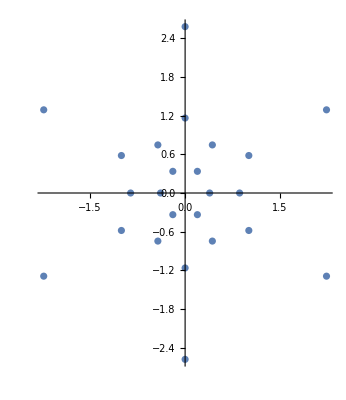

```mathematica
ComplexListPlot[Table[r[i],{i,24}]]
```

```mathematica
(*SL(5,C)Matrix normalization*)
```

```mathematica
m=s[25]+Sum[s[i]*(r[i]),{i,24}]/(-234.82807783353132-36.23261938468167 ⅈ)^(0.2)
```

{{1.96685+0.526152 ⅈ,-0.0535435-0.558684 ⅈ,-0.53941+0.155021 ⅈ,0.544653+0.135453 ⅈ,0.325712+0.457063 ⅈ},{-0.696763-0.996567 ⅈ,1.19087+0.468544 ⅈ,-0.181783-0.0452087 ⅈ,0.15083-0.277759 ⅈ,0.0178706+0.186466 ⅈ},{-1.18263-0.282862 ⅈ,-0.294628-0.279116 ⅈ,1.30777-0.0645636 ⅈ,-0.332613+0.232551 ⅈ,0.296986-0.108162 ⅈ},{-0.882756-0.83628 ⅈ,-0.108162-0.296986 ⅈ,-0.186466+0.0178706 ⅈ,-0.26001-0.50421 ⅈ,-0.279116+0.294628 ⅈ},{-1.1017-0.514671 ⅈ,-0.232551-0.332613 ⅈ,-0.277759-0.15083 ⅈ,0.0452087-0.181783 ⅈ,0.704158-0.613227 ⅈ}}

```mathematica
Det[m]
Tr[m]
```

1.03022+0.223144 ⅈ

4.90964-0.187304 ⅈ

```mathematica
msl=ExpandAll[s[25]+Sum[s[i]*(z-r[i]),{i,24}]/(-234.82807783353132-36.23261938468167 ⅈ)^(0.2)]
```

{{(0.0331489-0.526152 ⅈ)+(0.638794+0.43487 ⅈ) z,(0.0535435+0.558684 ⅈ)+(0.0883583+0.465209 ⅈ) z,(0.53941-0.155021 ⅈ)+(0.465209-0.0883583 ⅈ) z,(-0.544653-0.135453 ⅈ)+(0.0883583+0.465209 ⅈ) z,(-0.325712-0.457063 ⅈ)+(0.465209-0.0883583 ⅈ) z},{(0.696763+0.996567 ⅈ)+(0.465209-0.0883583 ⅈ) z,(0.809134-0.468544 ⅈ)+(0.0852269+0.0580197 ⅈ) z,(0.181783+0.0452087 ⅈ)+(0.0883583+0.465209 ⅈ) z,(-0.15083+0.277759 ⅈ)+(0.465209-0.0883583 ⅈ) z,(-0.0178706-0.186466 ⅈ)+(0.0883583+0.465209 ⅈ) z},{(1.18263+0.282862 ⅈ)+(0.0883583+0.465209 ⅈ) z,(0.294628+0.279116 ⅈ)+(0.465209-0.0883583 ⅈ) z,(0.692227+0.0645636 ⅈ)-(0.0818306+0.0557076 ⅈ) z,(0.332613-0.232551 ⅈ)+(0.0883583+0.465209 ⅈ) z,(-0.296986+0.108162 ⅈ)+(0.465209-0.0883583 ⅈ) z},{(0.882756+0.83628 ⅈ)+(0.465209-0.0883583 ⅈ) z,(0.108162+0.296986 ⅈ)+(0.0883583+0.465209 ⅈ) z,(0.186466-0.0178706 ⅈ)+(0.465209-0.0883583 ⅈ) z,(2.26001+0.50421 ⅈ)-(0.49059+0.333977 ⅈ) z,(0.279116-0.294628 ⅈ)+(0.0883583+0.465209 ⅈ) z},{(1.1017+0.514671 ⅈ)+(0.0883583+0.465209 ⅈ) z,(0.232551+0.332613 ⅈ)+(0.465209-0.0883583 ⅈ) z,(0.277759+0.15083 ⅈ)+(0.0883583+0.465209 ⅈ) z,(-0.0452087+0.181783 ⅈ)+(0.465209-0.0883583 ⅈ) z,(1.29584+0.613227 ⅈ)-(0.299548+0.203922 ⅈ) z}}

```mathematica
TableForm[msl]
```

(0.0331489-0.526152 ⅈ)+(0.638794+0.43487 ⅈ) z | (0.0535435+0.558684 ⅈ)+(0.0883583+0.465209 ⅈ) z | (0.53941-0.155021 ⅈ)+(0.465209-0.0883583 ⅈ) z | (-0.544653-0.135453 ⅈ)+(0.0883583+0.465209 ⅈ) z | (-0.325712-0.457063 ⅈ)+(0.465209-0.0883583 ⅈ) z
(0.696763+0.996567 ⅈ)+(0.465209-0.0883583 ⅈ) z | (0.809134-0.468544 ⅈ)+(0.0852269+0.0580197 ⅈ) z | (0.181783+0.0452087 ⅈ)+(0.0883583+0.465209 ⅈ) z | (-0.15083+0.277759 ⅈ)+(0.465209-0.0883583 ⅈ) z | (-0.0178706-0.186466 ⅈ)+(0.0883583+0.465209 ⅈ) z
(1.18263+0.282862 ⅈ)+(0.0883583+0.465209 ⅈ) z | (0.294628+0.279116 ⅈ)+(0.465209-0.0883583 ⅈ) z | (0.692227+0.0645636 ⅈ)-(0.0818306+0.0557076 ⅈ) z | (0.332613-0.232551 ⅈ)+(0.0883583+0.465209 ⅈ) z | (-0.296986+0.108162 ⅈ)+(0.465209-0.0883583 ⅈ) z
(0.882756+0.83628 ⅈ)+(0.465209-0.0883583 ⅈ) z | (0.108162+0.296986 ⅈ)+(0.0883583+0.465209 ⅈ) z | (0.186466-0.0178706 ⅈ)+(0.465209-0.0883583 ⅈ) z | (2.26001+0.50421 ⅈ)-(0.49059+0.333977 ⅈ) z | (0.279116-0.294628 ⅈ)+(0.0883583+0.465209 ⅈ) z
(1.1017+0.514671 ⅈ)+(0.0883583+0.465209 ⅈ) z | (0.232551+0.332613 ⅈ)+(0.465209-0.0883583 ⅈ) z | (0.277759+0.15083 ⅈ)+(0.0883583+0.465209 ⅈ) z | (-0.0452087+0.181783 ⅈ)+(0.465209-0.0883583 ⅈ) z | (1.29584+0.613227 ⅈ)-(0.299548+0.203922 ⅈ) z

```mathematica
f[z_]=ExpandAll[CharacteristicPolynomial[msl,z]/(0.8289647154558466+2.0800377828684953 ⅈ)]//Chop
```

(0.556277+0.0720402 ⅈ)-(1.6893-2.07348 ⅈ) z+(1.58681-4.15844 ⅈ) z^2-(0.0916832-3.1212 ⅈ) z^3-(1.5792+0.862583 ⅈ) z^4+1. z^5

```mathematica
w=z/.NSolve[f[z]==0,z]
```

{-1.23449+1.16296 ⅈ,0.0415172+0.24831 ⅈ,0.656536-0.895615 ⅈ,0.812486+0.403043 ⅈ,1.30315-0.0561131 ⅈ}

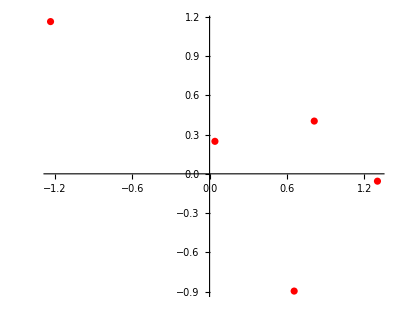

```mathematica
ComplexListPlot[w,PlotStyle->Red]
```

```mathematica
max2=Max[Norm/@w]+0.25
```

1.946

```mathematica
ga=ComplexPlot[f[z],{z,-max-I*max,max+I*max},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
gb=ComplexPlot3D[f[z],{z,-max-I*max,max+I*max},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
(*g1=JuliaSetPlot[f[x],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
g2=ListPlot[JuliaSetPoints[f[x],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All];
Export["Julia_SU5_6Dodecahedron_Polynomial_grid.jpg",GraphicsGrid[{{ga,gb}, 
 {g1,g2}},ImageSize->4000]]
"Julia_SU5_6Dodecahedron_Polynomial_grid.jpg"*)
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Sept 20026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz];
		
    
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-max2,max2,1000},{-max2,max2,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→"Rainbow",Background→Black,ViewPoint→Above,ImageSize->{2000,2000}];
```

```mathematica
Export["j_1000_SU5_6Docecahedron_Polynomial2_In_Out_monitor_g1.jpg",g1]
```

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> (Hue[1.75*#]&),ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU5_6Docecahedron_Polynomial2_In_Out_monitor_g2.jpg",g2]
```

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU5_6Docecahedron_Polynomial2_In_Out_monitor_g3.jpg",g3]
```

```mathematica
Export["j_1000_SU5_6Docecahedron_Polynomial2_grid.jpg",GraphicsGrid[{{ga,g2}, 
 {g3,g1}},ImageSize->4000]]
```

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear[s,w]
```

```mathematica
(*First so(5)*)
s[1]={{0,1,0,0,0},
           {1,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[2]={{0,0,1,0,0},
           {0,0,0,0,0},
          {1,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[3]={{0,0,0,1,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0},
{0,0,0,0,0}};
s[4]={{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0}};
s[5]={{0,0,0,0,0},
{0,0,1,0,0},
{0,1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[10]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,1},
        { 0,0,0,1,0}};
s[9]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,1,0,0}};
s[8]={{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,1,0,0,0}};
s[7]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,1,0},
{0,0,1,0,0},
{0,0,0,0,0}};
s[6]={{0,0,0,0,0},
{0,0,0,1,0},
{0,0,0,0,0},
{0,1,0,0,0},
{0,0,0,0,0}};
(* second so(5) *)
s[11]={{0,I,0,0,0},
           {-I,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[12]={{0,0,-I,0,0},
           {0,0,0,0,0},
          {I,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[13]={{0,0,0,I,0},
{0,0,0,0,0},
{0,0,0,0,0},
{-I,0,0,0,0},
{0,0,0,0,0}};
s[14]={{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{I,0,0,0,0}};
s[15]={{0,0,0,0,0},
{0,0,I,0,0},
{0,-I,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[20]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,I},
        { 0,0,0,-I,0}};
s[19]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,I,0,0}};
s[18]={{0,0,0,0,0},
{0,0,0,0,I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,-I,0,0,0}};
s[17]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,I,0},
{0,0,-I,0,0},
{0,0,0,0,0}};
s[16]={{0,0,0,0,0},
{0,0,0,-I,0},
{0,0,0,0,0},
{0,I,0,0,0},
{0,0,0,0,0}};
(* DIAGONAL four: n-1 matrices*)
(* zero trace with normalization Sqrt[n*(n-1)/2]*)
s[21]={{1,0,0,0,0},
{0,-1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[22]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,-2,0,0},
{0,0,0,0,0},
{0,0,0,0,-1}}/Sqrt[7/2];
s[23]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,-3,0},
{0,0,0,0,0}}/Sqrt[6];
s[24]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,1,0},
{0,0,0,0,-4}}/Sqrt[10];
s[25]=IdentityMatrix[5];
```

```mathematica
p[x_]=-1+296 x^6-602 x^12-296 x^18-x^24
```

-1+296 x^6-602 x^12-296 x^18-x^24

```mathematica
r[i_]:=z/.NSolve[p[z]==0,z][[i]]
```

```mathematica
ComplexListPlot[Table[r[i],{i,24}]]
```

-Graphics-

```mathematica
(*SL(5,C)Matrix normalization*)
```

```mathematica
m=s[25]+Sum[s[i]*(r[i]),{i,24}]/(-182.95282973555163+97.62071768248362 ⅈ)^(0.2)
```

{{1.87083-0.665754 ⅈ,-0.542308-0.196276 ⅈ,-0.093569+0.569093 ⅈ,0.365579-0.446064 ⅈ,0.56779-0.101174 ⅈ},{-1.23209+0.208145 ⅈ,1.47567+0.0293751 ⅈ,-0.122015+0.148878 ⅈ,-0.191486-0.262342 ⅈ,0.181+0.0655087 ⅈ},{-0.783349+0.973514 ⅈ,-0.388881+0.150663 ⅈ,1.03216-0.313901 ⅈ,0.0694703+0.41122 ⅈ,0.0303369-0.323373 ⅈ},{-1.16516+0.451413 ⅈ,-0.323373-0.0303369 ⅈ,-0.0655087+0.181 ⅈ,0.743556+0.942773 ⅈ,0.150663+0.388881 ⅈ},{-0.962947+0.796303 ⅈ,-0.41122+0.0694703 ⅈ,-0.262342+0.191486 ⅈ,-0.148878-0.122015 ⅈ,-0.335922+0.00893645 ⅈ}}

```mathematica
Det[m]
Tr[m]
```

0.529937-0.905913 ⅈ

4.7863+0.00142949 ⅈ

```mathematica
msl=ExpandAll[s[25]+Sum[s[i]*(z-r[i]),{i,24}]/(-182.95282973555163+97.62071768248362 ⅈ)^(0.2)]
```

{{(0.129169+0.665754 ⅈ)+(0.670514-0.393125 ⅈ) z,(0.542308+0.196276 ⅈ)+(0.470845+0.122793 ⅈ) z,(0.093569-0.569093 ⅈ)+(0.122793-0.470845 ⅈ) z,(-0.365579+0.446064 ⅈ)+(0.470845+0.122793 ⅈ) z,(-0.56779+0.101174 ⅈ)+(0.122793-0.470845 ⅈ) z},{(1.23209-0.208145 ⅈ)+(0.122793-0.470845 ⅈ) z,(0.524325-0.0293751 ⅈ)+(0.0768757-0.0450726 ⅈ) z,(0.122015-0.148878 ⅈ)+(0.470845+0.122793 ⅈ) z,(0.191486+0.262342 ⅈ)+(0.122793-0.470845 ⅈ) z,(-0.181-0.0655087 ⅈ)+(0.470845+0.122793 ⅈ) z},{(0.783349-0.973514 ⅈ)+(0.470845+0.122793 ⅈ) z,(0.388881-0.150663 ⅈ)+(0.122793-0.470845 ⅈ) z,(0.967836+0.313901 ⅈ)-(0.102275-0.059964 ⅈ) z,(-0.0694703-0.41122 ⅈ)+(0.470845+0.122793 ⅈ) z,(-0.0303369+0.323373 ⅈ)+(0.122793-0.470845 ⅈ) z},{(1.16516-0.451413 ⅈ)+(0.122793-0.470845 ⅈ) z,(0.323373+0.0303369 ⅈ)+(0.470845+0.122793 ⅈ) z,(0.0655087-0.181 ⅈ)+(0.122793-0.470845 ⅈ) z,(1.25644-0.942773 ⅈ)-(0.269665-0.158106 ⅈ) z,(-0.150663-0.388881 ⅈ)+(0.470845+0.122793 ⅈ) z},{(0.962947-0.796303 ⅈ)+(0.470845+0.122793 ⅈ) z,(0.41122-0.0694703 ⅈ)+(0.122793-0.470845 ⅈ) z,(0.262342-0.191486 ⅈ)+(0.470845+0.122793 ⅈ) z,(0.148878+0.122015 ⅈ)+(0.122793-0.470845 ⅈ) z,(2.33592-0.00893645 ⅈ)-(0.534106-0.313149 ⅈ) z}}

```mathematica
TableForm[msl]
```

(0.129169+0.665754 ⅈ)+(0.670514-0.393125 ⅈ) z | (0.542308+0.196276 ⅈ)+(0.470845+0.122793 ⅈ) z | (0.093569-0.569093 ⅈ)+(0.122793-0.470845 ⅈ) z | (-0.365579+0.446064 ⅈ)+(0.470845+0.122793 ⅈ) z | (-0.56779+0.101174 ⅈ)+(0.122793-0.470845 ⅈ) z
(1.23209-0.208145 ⅈ)+(0.122793-0.470845 ⅈ) z | (0.524325-0.0293751 ⅈ)+(0.0768757-0.0450726 ⅈ) z | (0.122015-0.148878 ⅈ)+(0.470845+0.122793 ⅈ) z | (0.191486+0.262342 ⅈ)+(0.122793-0.470845 ⅈ) z | (-0.181-0.0655087 ⅈ)+(0.470845+0.122793 ⅈ) z
(0.783349-0.973514 ⅈ)+(0.470845+0.122793 ⅈ) z | (0.388881-0.150663 ⅈ)+(0.122793-0.470845 ⅈ) z | (0.967836+0.313901 ⅈ)-(0.102275-0.059964 ⅈ) z | (-0.0694703-0.41122 ⅈ)+(0.470845+0.122793 ⅈ) z | (-0.0303369+0.323373 ⅈ)+(0.122793-0.470845 ⅈ) z
(1.16516-0.451413 ⅈ)+(0.122793-0.470845 ⅈ) z | (0.323373+0.0303369 ⅈ)+(0.470845+0.122793 ⅈ) z | (0.0655087-0.181 ⅈ)+(0.122793-0.470845 ⅈ) z | (1.25644-0.942773 ⅈ)-(0.269665-0.158106 ⅈ) z | (-0.150663-0.388881 ⅈ)+(0.470845+0.122793 ⅈ) z
(0.962947-0.796303 ⅈ)+(0.470845+0.122793 ⅈ) z | (0.41122-0.0694703 ⅈ)+(0.122793-0.470845 ⅈ) z | (0.262342-0.191486 ⅈ)+(0.470845+0.122793 ⅈ) z | (0.148878+0.122015 ⅈ)+(0.122793-0.470845 ⅈ) z | (2.33592-0.00893645 ⅈ)-(0.534106-0.313149 ⅈ) z

```mathematica
f[z_]=ExpandAll[CharacteristicPolynomial[msl,z]/(1.0447083447321037-1.745631911294754 ⅈ)*((0.5562767723321311+0.07204020823194279 ⅈ)-(1.6892981599671266-2.073482233079483 ⅈ) z+(1.5868125411192382-4.158435062905627 ⅈ) z^2-(0.09168322272134899-3.1212008548162022 ⅈ) z^3-(1.5792028100184778+0.8625831670296813 ⅈ) z^4+1. z^5)]//Chop
```

(-0.462064-0.36296 ⅈ)+(2.6851-2.15598 ⅈ) z+(1.76872+9.38007 ⅈ) z^2-(22.5568+13.5747 ⅈ) z^3+(45.2002+9.07111 ⅈ) z^4-(42.1448+0.969402 ⅈ) z^5+(18.6602-4.29876 ⅈ) z^6-(3.32618-5.1328 ⅈ) z^7+(2.6616-2.66051 ⅈ) z^8-(3.17278-0.466685 ⅈ) z^9+1. z^10

```mathematica
w=z/.NSolve[f[z]==0,z]
```

{-1.4731-1.74161 ⅈ,-1.23449+1.16296 ⅈ,-0.237025+0.139158 ⅈ,0.0415172+0.24831 ⅈ,0.656536-0.895615 ⅈ,0.788846+0.578253 ⅈ,0.812486+0.403043 ⅈ,0.844315-0.556407 ⅈ,1.30315-0.0561131 ⅈ,1.67054+0.251339 ⅈ}

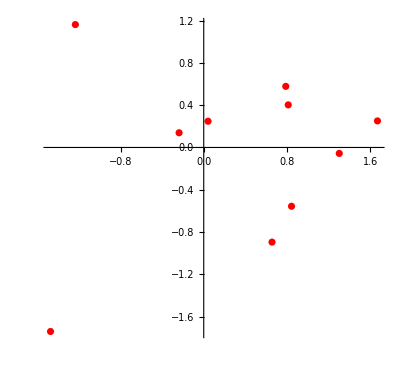

```mathematica
ComplexListPlot[w,PlotStyle->Red]
```

```mathematica
max2=Max[Norm/@w]+0.25
```

2.53106

```mathematica
ga=ComplexPlot[f[z],{z,-max-I*max,max+I*max},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
gb=ComplexPlot3D[f[z],{z,-max-I*max,max+I*max},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100,ViewPoint->Above];
```

```mathematica
Export["ComplexPlot_SU5_6Docecahedron_Polynomial_deSitter_Anti_deSitter_In_Out_monitor_gagb.jpg",{ga,gb}]
```

ComplexPlot_SU5_6Docecahedron_Polynomial_deSitter_Anti_deSitter_In_Out_monitor_gagb.jpg

```mathematica
(*g1=JuliaSetPlot[f[x],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
g2=ListPlot[JuliaSetPoints[f[x],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All];
Export["Julia_SU5_6Dodecahedron_Polynomial_grid.jpg",GraphicsGrid[{{ga,gb}, 
 {g1,g2}},ImageSize->4000]]
"Julia_SU5_6Dodecahedron_Polynomial_grid.jpg"*)
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Sept 20026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz];
		
    
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-max2,max2,1000},{-max2,max2,1000}}];
```

General::munfl: (-1.71606-1.71606 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.711-1.711 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.711-1.711 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-0.809939-0.809939 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.420156-0.420156 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.711+1.711 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.711+1.711 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.59963+1.59963 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→"Rainbow",Background→Black,ViewPoint→Above,ImageSize->{2000,2000}];
```

```mathematica
Export["j_1000_SU5_6Docecahedron_Polynomial_deSitter_Anti_deSitter_In_Out_monitor_g1.jpg",g1]
```

j_1000_SU5_6Docecahedron_Polynomial_deSitter_Anti_deSitter_In_Out_monitor_g1.jpg

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> (Hue[1.75*#]&),ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU5_6Docecahedron_Polynomial_deSitter_In_Out_monitor_g2.jpg",g2]
```

j_1000_SU5_6Docecahedron_Polynomial_deSitter_In_Out_monitor_g2.jpg

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU5_6Docecahedron_Polynomial_deSitter_Anti_deSitter_In_Out_monitor_g3.jpg",g3]
```

j_1000_SU5_6Docecahedron_Polynomial_deSitter_Anti_deSitter_In_Out_monitor_g3.jpg

```mathematica
Export["j_1000_SU5_6Docecahedron_Polynomial_deSitter_Anti_deSitter_grid.jpg",GraphicsGrid[{{ga,g2}, 
 {g3,g1}},ImageSize->4000]]
```

j_1000_SU5_6Docecahedron_Polynomial_deSitter_Anti_deSitter_grid.jpg

```mathematica
(*end*)
```